```mathematica
ClearAll["Global`*"];
If[Length[$FrontEnd]>0,SetDirectory[NotebookDirectory[]]];
<<Equiprobable-Returns-Functions.m;
```

```mathematica
𝓇1=0.02;
𝓇2=0.022;
𝓍=0.2;
Σ=0.3;
ρ=2;
```

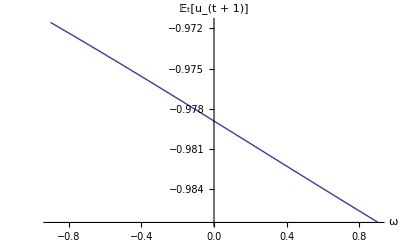

{{Equiprobable,0.72568}}

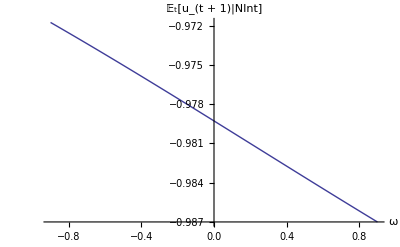

{{Equiprobable,0.72568},{Direct,10.37588}}

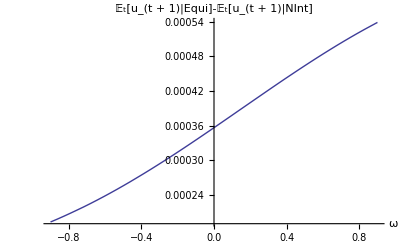

{{Equiprobable,0.72568},{Direct,10.37588},{Difference,11.29707}}

(Equiprobable | 0.72568
Direct | 10.37588
Difference | 11.29707)

```mathematica
ϛ = 0.5;
𝔼uEquiSetup[NumOfPoints=20];
Get["./uExpectedByMethod.m"];
Clear[ϛ];
```

```mathematica
ω=0.5;
Get["./ShareByCRRA.m"];
Clear[ω];
```

```mathematica
(* Now examine results for ρ=2 and varying ω *)
```

{{Direct,5295.73459}}

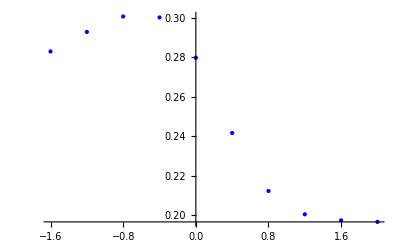

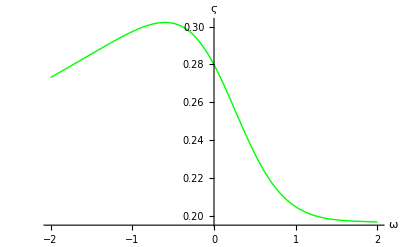

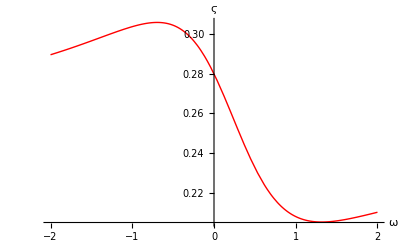

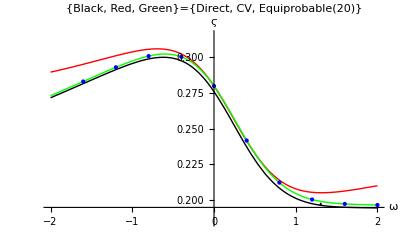

(Direct | 5295.73459
EquiprobableList | 0.974271
Equiprobable | 40.67532
CVApprox | 0.01725)

```mathematica
Clear[ϛ,ω];
{ωMinPlot,ωMaxPlot}={-2.,2.};ωGap=(ωMaxPlot-ωMinPlot);
ρ=2.;
𝔼uEquiSetup[NumOfPoints=20];
Get["./ShareVsCovByMethod.m"];
```